# This Notebook is part of the Supporting Information for: “Equibiaxial elongation of entangled polyisobutylene melts: Experiments and theoretical predictions” Seyed Mahmoud Arzideh, Andrés Córdoba, Jeffrey G. Ethier, Jay D. Schieber, and David C. Venerus

## Accepted for publication in the Journal of Rheology on March 2024 email: andcorduri@gmail.com (Andrés Córdoba)

## Definition of Functions

```mathematica
(*The Rolie-Double-Poly (RP) model, Boudara et. al., J.Rheol.63(1),71–91*)
Clear[RDPmodel]
RDPmodel[ϵd0_?NumericQ,m_?NumericQ,MWDist_?MatrixQ,Me_?NumericQ,τe_?NumericQ,GN0_?NumericQ,λmax_?NumericQ,rang_?ArrayQ,ICin_?ArrayQ]:=Module[{κ,c,dγ,cxx,cyx,cxy,cyy,czz,RHS,ec1,ec2,ec3,IC,crelax,sol,cond,nm,Z,C1=1.69,C2=4.17,C3=-1.55,τd,τs,Rrep,RCR,Rret,βth=1,βCCR=1,δ=-1/2,RCCR,res1,res2,res3,sampl,dfdc,entropyg,R=8.3145,A,res1b,res1c,resRrep,resRCR,resRret,resRCCR,rescrelax,t},
Z=#[[1]]/Me&/@MWDist;
nm=Length[MWDist];
τd=3#^3 τe (1-(2C1)/#^(1/2)+C2/#+C3/#^(3/2))&/@Z;
τs=#^2 τe&/@Z;
c=Table[{{cxx[i,j][t],0,0},{0,cyy[i,j][t],0},{0,0,czz[i,j][t]}},{i,1,nm},{j,nm}];
A=Table[Sum[MWDist[[j,2]]*c[[i,j]],{j,1,nm}],{i,1,nm}];
κ=ϵd0*{{1,0,0},{0,m,0},{0,0,-(1+m)}};
Rrep=Table[(1/τd[[i]])(c[[i,j]]-IdentityMatrix[3]),{i,1,nm},{j,1,nm}];
RCR=Table[(βth/τd[[j]])(c[[i,j]]-IdentityMatrix[3]),{i,1,nm},{j,1,nm}];
Rret=Table[((2(1-(Tr[A[[i]]]/3)^(-1/2)))/τs[[i]])((1-λmax^-2)/(1-(Tr[A[[i]]]/3)λmax^-2))c[[i,j]],{i,1,nm},
{j,1nm}];
RCCR=Table[2 βCCR ((1-(Tr[A[[j]]]/3)^(-1/2))/τs[[j]])((1-λmax^-2)/(1-(Tr[A[[j]]]/3)λmax^-2))(Tr[A[[i]]]/3)^δ(c[[i,j]]-IdentityMatrix[3]),{i,1,nm},{j,1,nm}];
crelax=-(Rrep+RCR+Rret+RCCR);
RHS=Table[κ.(c[[i,j]])+(c[[i,j]]).Transpose[κ],{i,1,nm},{j,1,nm}]+crelax;
ec1=Flatten[Table[Drop[Sort[Flatten[MapThread[#1==#2&,{D[c[[i,j]],t],RHS[[i,j]]},2]]],6],{i,1,nm},{j,1,nm}]];
IC=Flatten[Table[{(cxx[i,j][t]/.t->0)==ICin[[i,j,1]],(cyy[i,j][t]/.t->0)==ICin[[i,j,2]],(czz[i,j][t]/.t->0)==ICin[[i,j,3]]},{i,1,nm},{j,1,nm}]];
sol=NDSolve[Join[ec1,IC],Flatten[Diagonal[#]&/@Flatten[c,1]],{t,0,rang[[2]]}][[1]];
sampl=Exp[Table[i,{i,N[Log[rang[[1]]]],N[Log[rang[[2]]]],(N[Log[rang[[2]]]]-N[Log[rang[[1]]]])/100}]];
res1=A/.sol/.t->#&/@sampl;
res1b=Table[Inverse[#[[i]]],{i,1,nm}]&/@res1;
res1c=Table[Tr[#[[i]]],{i,1,nm}]&/@res1;
resRrep=Table[(1/τd[[i]])((c[[i,j]]/.sol)-IdentityMatrix[3]),{i,1,nm},{j,1,nm}]/.t->#&/@sampl;
resRCR=Table[(βth/τd[[j]])((c[[i,j]]/.sol)-IdentityMatrix[3]),{i,1,nm},{j,1,nm}]/.t->#&/@sampl;
resRret=MapThread[Table[((2(1-(#2[[i]]/3)^(-1/2)))/τs[[i]])((1-λmax^-2)/(1-(#2[[i]]/3)λmax^-2))(c[[i,j]]/.sol),{i,1,nm},
{j,1nm}]/.t->#1&,{sampl,res1c}];
resRCCR=MapThread[Table[2 βCCR ((1-(#2[[j]]/3)^(-1/2))/τs[[j]])((1-λmax^-2)/(1-(#2[[j]]/3)λmax^-2))(#2[[i]]/3)^δ((c[[i,j]]/.sol)-IdentityMatrix[3]),{i,1,nm},{j,1,nm}]/.t->#1&,{sampl,res1c}];
rescrelax=MapThread[-(#1+#2+#3+#4)&,{resRrep,resRCR,resRret,resRCCR}];
res2=Sum[MWDist[[i,2]]((1-λmax^-2)/(1-(Tr[#[[i]]]/3)λmax^-2))#[[i]],{i,1,nm}]&/@res1 ;
res3=MapThread[{#1,If[ϵd0>0,GN0(#2[[1,1]]-#2[[3,3]])/ϵd0,0]}&,{sampl,res2}];
entropyg=MapThread[{#1,-1/2 Sum[Sum[((Z[[i]]R MWDist[[i,2]])/MWDist[[i,1]])((((1-λmax^-2)/(1-(#3[[i]]/3)λmax^-2))KroneckerDelta[k,l])-#2[[i,k,l]])*If[i==j,MWDist[[i,2]],MWDist[[j,2]]]*#4[[j,i,k,l]],{i,1,nm},{j,1,nm}],{k,1,3},{l,1,3}] }&,{sampl,res1b,res1c,rescrelax}];
{res3,entropyg,Table[{(cxx[i,j][t]/.sol/.t->Last[sampl]),(cyy[i,j][t]/.sol/.t->Last[sampl]),(czz[i,j][t]/.sol/.t->Last[sampl])},{i,1,nm},{j,nm}]}]
```

```mathematica
(*The Rolie-Double-Poly (RP) model, Boudara et. al., J.Rheol.63(1),71–91*)
Clear[RDPmodelC2]
RDPmodelC2[trc_?NumericQ,cxx_?NumericQ,MWDist_?MatrixQ,Me_?NumericQ,τe_?NumericQ,GN0_?NumericQ,λmax_?NumericQ]:=Module[{κ,c,dγ,cyx,cxy,cyy,czz,RHS,ec1,ec2,ec3,IC,crelax,sol,cond,nm,Z,C1=1.69,C2=4.17,C3=-1.55,τd,τs,Rrep,RCR,Rret,βth=1,βCCR=1,δ=-1/2,RCCR,res1,res2,res3,sampl,dfdc,entropyg,R=8.3145,A,res1b,res1c,resRrep,resRCR,resRret,resRCCR,rescrelax,t},
Z=#[[1]]/Me&/@MWDist;
nm=Length[MWDist];
τd=3#^3 τe (1-(2C1)/#^(1/2)+C2/#+C3/#^(3/2))&/@Z;
τs=#^2 τe&/@Z;
sol=Table[NSolve[{trc==cxx+cyy+czz,cyy==czz},{cyy,czz}],{i,1,nm},{j,1,nm}];
c=Table[{{cxx,0,0},{0,cyy,0},{0,0,czz}}/.sol[[i,j,1]],{i,1,nm},{j,nm}];
A=Table[MWDist[[i,2]]*c[[i,i]]+Sum[If[i≠j,MWDist[[j,2]]*c[[i,j]],0],{j,1,nm}],{i,1,nm}];
res1b=Table[Inverse[A[[i]]],{i,1,nm}];
res1c=Table[Tr[A[[i]]],{i,1,nm}];
resRrep=Table[(1/τd[[i]])(c[[i,j]]-IdentityMatrix[3]),{i,1,nm},{j,1,nm}];
resRCR=Table[(βth/τd[[j]])(c[[i,j]]-IdentityMatrix[3]),{i,1,nm},{j,1,nm}];
resRret=Table[((2(1-(res1c[[i]]/3)^(-1/2)))/τs[[i]])((1-λmax^-2)/(1-(res1c[[i]]/3)λmax^-2))c[[i,j]],{i,1,nm},{j,1nm}];
resRCCR=Table[2 βCCR ((1-(res1c[[j]]/3)^(-1/2))/τs[[j]])((1-λmax^-2)/(1-(res1c[[j]]/3)λmax^-2))(res1c[[i]]/3)^δ(c[[i,j]]-IdentityMatrix[3]),{i,1,nm},{j,1,nm}];
rescrelax=MapThread[-(#1+#2+#3+#4)&,{resRrep,resRCR,resRret,resRCCR}];
res2=Sum[MWDist[[i,2]]((1-λmax^-2)/(1-(Tr[A[[i]]]/3)λmax^-2))A[[i]],{i,1,nm}] ;
entropyg=-1/2 Sum[Sum[((Z[[i]]R MWDist[[i,2]])/MWDist[[i,1]])((((1-λmax^-2)/(1-(res1c[[i]]/3)λmax^-2))KroneckerDelta[k,l])-res1b[[i,k,l]])*If[i==j,MWDist[[i,2]],MWDist[[j,2]]]*rescrelax[[j,i,k,l]],{i,1,nm},{j,1,nm}],{k,1,3},{l,1,3}]]
```

```mathematica
Clear[PowerTicks]
PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i],Spacer[{0,0}]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}],{0.005,0.},{Thickness[0.001]}},{i,min10,max10},{k,9}],1]]]
```

```mathematica
Clear[ErrBarP]
(*The function "ErrBarP" is for plotting the error bars in a log-log plot*)
ErrBarP[data_/;MatrixQ[data,NumericQ],err_/;VectorQ[err,NumericQ],del_?NumericQ,color_]:=
Module[{data2,data3,err2},
data2=Select[MapThread[{#1[[1]],#1[[2]],#2}&,{data,err}],#[[2]]-#[[3]]>0&&#[[2]]+#[[3]]>0&];
data3={#[[1]],#[[2]]}&/@data2;err2=#[[3]]&/@data2;
{{color,MapThread[Line[{Log[{#1[[1]],(#1[[2]]-#2)}],Log[{#1[[1]],(#1[[2]]+#2)}]}]&,{data3,err2}]},{color,MapThread[Line[{{Log[#1[[1]]]-del,Log[(#1[[2]]-#2)]},{Log[#1[[1]]]+del,Log[(#1[[2]]-#2)]}}]&,{data3,err2}]},{color,MapThread[Line[{{Log[#1[[1]]]-del,Log[(#1[[2]]+ #2)]},{Log[#1[[1]]]+del,Log[(#1[[2]]+#2)]}}]&,{data3,err2}]}}]
```

## Sample calculations for the MW = 130 kDa and PDI = 1.14 system

```mathematica
(*Specifying the Molecular weight distribution*)
Mn=113.950;Mw=130.414;
Mmp=Mn^(5/2)/Mw^(3/2);soldist={μ->Log[Mn^(3/2)/(√Mw)],σ->√2 √Log[(√Mw)/(√Mn)],C[1]->0,C[2]->0};
cutoffdist=FindRoot[10^-4(PDF[LogNormalDistribution[μ,σ],Mmp]/.soldist)==PDF[LogNormalDistribution[μ,σ],xc]/.soldist,{xc,Mw}];
MCv=3000;
NCsAll={14,20,28,34,40,50,60,70,80,90};
NCsAllLimits=Append[Prepend[NCsAll,0],xc*1000/MCv/.cutoffdist];
MwRDP=Table[{Mean[{NCsAllLimits[[i]]*MCv/1000,NCsAllLimits[[i+1]]*MCv/1000}],NIntegrate[PDF[LogNormalDistribution[μ,σ],x]/.soldist,{x,NCsAllLimits[[i]]*MCv/1000,NCsAllLimits[[i+1]]*MCv/1000}]},{i,1,Length[NCsAllLimits]-1}];
```

```mathematica
(*Discretized form of the molecular weight distribution used in the calculations below*)
Prepend[MwRDP,{"M,kDa","fraction"}]//TableForm
```

M,kDa | fraction
21 | 0.00565072
51 | 0.0534548
72 | 0.199901
93 | 0.194069
111 | 0.174145
135 | 0.197091
165 | 0.0990743
195 | 0.0443009
225 | 0.0188062
255 | 0.007835
360.173 | 0.0056281

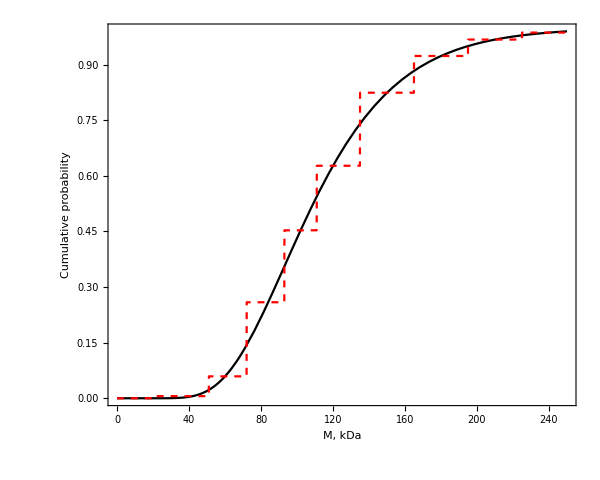

```mathematica
Quiet[Needs["PlotLegends`"]];
distD=EmpiricalDistribution[(#[[2]]&/@MwRDP)->(#[[1]]&/@MwRDP)];
Legend1={{{Graphics[{Black, Thick,Line[{{0,0},{3,0}}]}],Text[Style["Log-Normal distribution",FontSize->15,FontFamily->"Arial",Black]]},{Graphics[{Red,Dashed, Thick,Line[{{0,0},{3,0}}]}],Text[Style["Discretized version used in RDP",FontSize->15,FontFamily->"Arial",Black]]}},LegendShadow->False,LegendSize->{0.95,0.2},LegendPosition->{-0.76,0.56},LegendTextSpace->6,LegendBorder->False};
ShowLegend[Plot[{CDF[LogNormalDistribution[μ,σ],x]/.soldist/.{C[1]->0,C[2]->0}/.{Mn->113.950,Mw->130.414},CDF[distD,x]},{x,0,250},Frame->True,ImageSize->600,BaseStyle->{FontSize->21,FontFamily->"Arial"},FrameLabel->{"M, kDa","Cumulative probability"},PlotStyle->{Black,{Red,Dashed}},AspectRatio->0.8,Exclusions->None],Legend1]
```

```mathematica
(*Specifying the Parameters*)
mIn=1;(*This parameter defined the type of elongational flow, 1 is for biaxial, simple elongation is -1/2 and planar is 0. See Meissner et. al., J. Nonnewton. Fluid. Mech. ,11 (1982) 221-237*)
MeIn=6.690; (*Entanglement molecular weight in kDa, taken from Fetters et. al.*)
τeIn=3.5*10^-3;(*Rouse relaxation time of one entanglement
segment in seconds, Subscript[τ, e]. I chose this to be Subscript[τ, e]=0.502*Subscript[tau, c] based on Macromolecules,vol.54,pp.8033–8042,2021. Where Subscript[τ, c] is the cluster-shuffling characteristic time in CFSM*)
GN0In=308.165;(*The plateau modulus in kPa.*)
λmaxIn=2(*Maximum stretch ratio*);
```

### Inception of biaxial elongation

```mathematica
solϵdp3=RDPmodel[0.3,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^1},Table[{1,1,1},{i,1,Length[MwRDP]},{j,1,Length[MwRDP]}]];
```

```mathematica
solϵdp1=RDPmodel[0.1,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,5*10^1},Table[{1,1,1},{i,1,Length[MwRDP]},{j,1,Length[MwRDP]}]];
```

```mathematica
solϵdp03=RDPmodel[0.03,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Table[{1,1,1},{i,1,Length[MwRDP]},{j,1,Length[MwRDP]}]];
```

```mathematica
solϵdp01=RDPmodel[0.01,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,3.5*10^2},Table[{1,1,1},{i,1,Length[MwRDP]},{j,1,Length[MwRDP]}]];
```

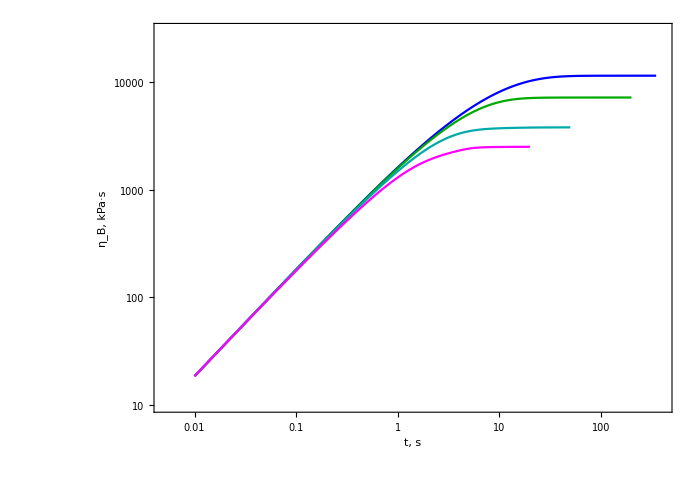

```mathematica
Quiet[Needs["PlotLegends`"]];
Legend1={{{Graphics[{Blue, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.01 s^-1",FontSize->16,FontFamily->"Arial",Blue]]},{Graphics[{Darker[Green], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.03 s^-1",FontSize->16,FontFamily->"Arial",Darker[Green]]]},{Graphics[{Darker[Cyan], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.1 s^-1",FontSize->16,FontFamily->"Arial",Darker[Cyan]]]},{Graphics[{Magenta, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.3 s^-1",FontSize->16,FontFamily->"Arial",Magenta]]}},LegendShadow->False,LegendSize->{0.63,0.3},LegendPosition->{-0.76,0.35},LegendTextSpace->4,LegendBorder->False};
ShowLegend[ListLogLogPlot[{solϵdp01[[1]],solϵdp03[[1]],solϵdp1[[1]],solϵdp3[[1]]},PlotRange->{{0.5*10^-2,4*10^2},{1*10^1,3*10^4}},Frame->True,Axes->False,BaseStyle->{FontSize->22,FontFamily->"Arial"},AspectRatio->0.7,FrameLabel->{"t, s","η_B, kPa·s"},ImageSize->700,Joined->True,PlotStyle->{{Blue},{Darker[Green]},{Darker[Cyan]},Magenta},FrameTicks->{{PowerTicks[True],PowerTicks[False]},{PowerTicks[True],PowerTicks[False]}}],Legend1]
```

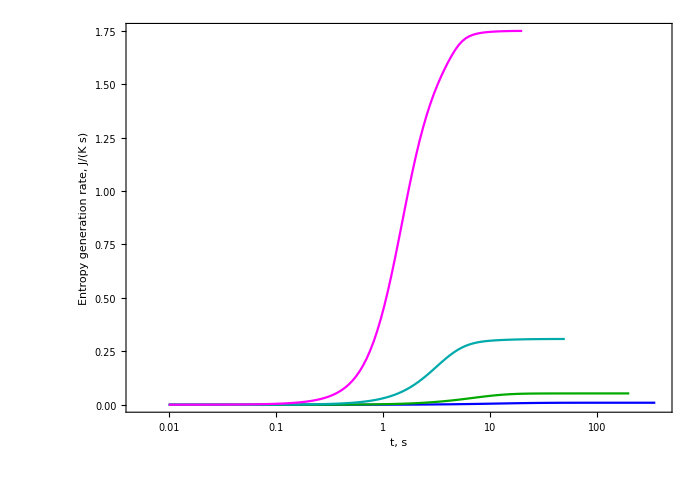

```mathematica
Quiet[Needs["PlotLegends`"]];
Legend1={{{Graphics[{Blue, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.01 s^-1",FontSize->16,FontFamily->"Arial",Blue]]},{Graphics[{Darker[Green], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.03 s^-1",FontSize->16,FontFamily->"Arial",Darker[Green]]]},{Graphics[{Darker[Cyan], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.1 s^-1",FontSize->16,FontFamily->"Arial",Darker[Cyan]]]},{Graphics[{Magenta, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.3 s^-1",FontSize->16,FontFamily->"Arial",Magenta]]}},LegendShadow->False,LegendSize->{0.63,0.3},LegendPosition->{-0.74,0.35},LegendTextSpace->4,LegendBorder->False};
InsetP1=ListLogLinearPlot[{solϵdp01[[2]],solϵdp03[[2]]},PlotRange->{{0.5*10^-2,4*10^2},All},Frame->True,Axes->False,BaseStyle->{FontSize->10,FontFamily->"Arial"},AspectRatio->0.7,FrameLabel->{"t, seconds","Entropy generation rate, J/(K s)"},ImageSize->230,Joined->True,PlotStyle->{{Blue},{Darker[Green]},{Darker[Cyan]},Magenta},FrameTicks->{{Automatic,Automatic},{PowerTicks[True],PowerTicks[False]}}];
ShowLegend[ListLogLinearPlot[{solϵdp01[[2]],solϵdp03[[2]],solϵdp1[[2]],solϵdp3[[2]]},PlotRange->{{0.5*10^-2,4*10^2},All},Frame->True,Axes->False,BaseStyle->{FontSize->22,FontFamily->"Arial"},AspectRatio->0.7,FrameLabel->{"t, s","Entropy generation rate, J/(K s)"},ImageSize->700,Joined->True,PlotStyle->{{Blue},{Darker[Green]},{Darker[Cyan]},Magenta},Epilog->Inset[InsetP1,{Log[4*10^1],0.9}],FrameTicks->{{Automatic,Automatic},{PowerTicks[True],PowerTicks[False]}}],Legend1]
```

### Cessation after biaxial elongation

```mathematica
solϵdp3c=RDPmodel[0,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp3]];
```

```mathematica
solϵdp1c=RDPmodel[0,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp1]];
```

```mathematica
solϵdp03c=RDPmodel[0,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp03]];
```

```mathematica
solϵdp01c=RDPmodel[0,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp01]];
```

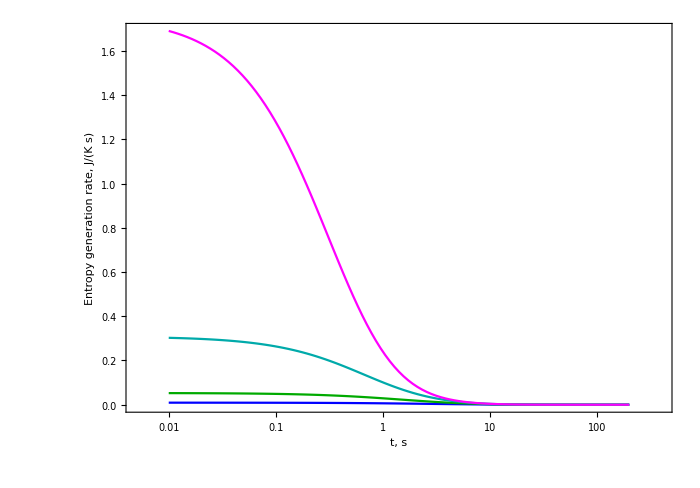

```mathematica
Quiet[Needs["PlotLegends`"]];
Legend1={{{Graphics[{Blue, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.01 s^-1",FontSize->16,FontFamily->"Arial",Blue]]},{Graphics[{Darker[Green], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.03 s^-1",FontSize->16,FontFamily->"Arial",Darker[Green]]]},{Graphics[{Darker[Cyan], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.1 s^-1",FontSize->16,FontFamily->"Arial",Darker[Cyan]]]},{Graphics[{Magenta, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=0.3 s^-1",FontSize->16,FontFamily->"Arial",Magenta]]}},LegendShadow->False,LegendSize->{0.63,0.3},LegendPosition->{-0.3,0.35},LegendTextSpace->4,LegendBorder->False};
InsetP1=ListLogLinearPlot[{solϵdp01c[[2]],solϵdp03c[[2]]},PlotRange->{{0.5*10^-2,4*10^2},All},Frame->True,Axes->False,BaseStyle->{FontSize->10,FontFamily->"Arial"},AspectRatio->0.7,FrameLabel->{"t, seconds","Entropy generation rate, J/(K s)"},ImageSize->230,Joined->True,PlotStyle->{{Blue},{Darker[Green]},{Darker[Cyan]},Magenta},FrameTicks->{{Automatic,Automatic},{PowerTicks[True],PowerTicks[False]}}];
ShowLegend[ListLogLinearPlot[{solϵdp01c[[2]],solϵdp03c[[2]],solϵdp1c[[2]],solϵdp3c[[2]]},PlotRange->{{0.5*10^-2,4*10^2},All},Frame->True,Axes->False,BaseStyle->{FontSize->22,FontFamily->"Arial"},AspectRatio->0.7,FrameLabel->{"t, s","Entropy generation rate, J/(K s)"},ImageSize->700,Joined->True,PlotStyle->{{Blue},{Darker[Green]},{Darker[Cyan]},Magenta},Epilog->Inset[InsetP1,{Log[4*10^1],0.9}],FrameTicks->{{Automatic,Automatic},{PowerTicks[True],PowerTicks[False]}}],Legend1]
```

### Sudden reversal after biaxial elongation

```mathematica
solϵdp3r=RDPmodel[-0.3,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp3]];
```

```mathematica
solϵdp1r=RDPmodel[-0.1,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp1]];
```

```mathematica
solϵdp03r=RDPmodel[-0.03,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp03]];
```

```mathematica
solϵdp01r=RDPmodel[-0.01,mIn,MwRDP,MeIn,τeIn,GN0In,λmaxIn,{10^-2,2*10^2},Last[solϵdp01]];
```

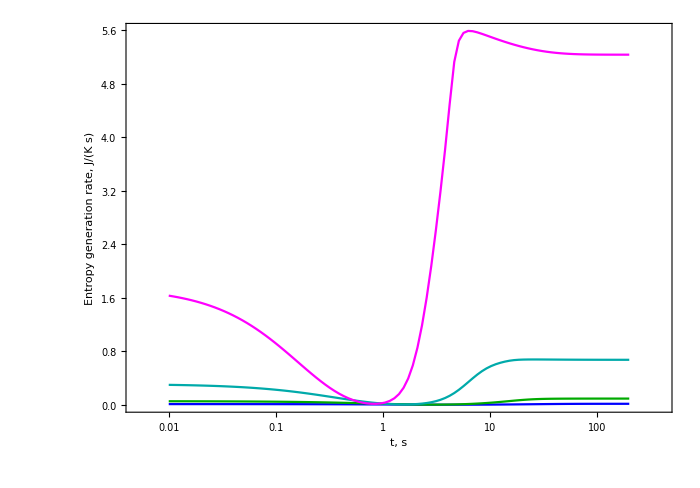

```mathematica
Quiet[Needs["PlotLegends`"]];
Legend1={{{Graphics[{Blue, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=-0.01 s^-1",FontSize->16,FontFamily->"Arial",Blue]]},{Graphics[{Darker[Green], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=-0.03 s^-1",FontSize->16,FontFamily->"Arial",Darker[Green]]]},{Graphics[{Darker[Cyan], Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=-0.1 s^-1",FontSize->16,FontFamily->"Arial",Darker[Cyan]]]},{Graphics[{Magenta, Thick,Line[{{0,0},{6,0}}]}],Text[Style["RDP,OverDot[SubscriptBox[ϵ, B]]=-0.3 s^-1",FontSize->16,FontFamily->"Arial",Magenta]]}},LegendShadow->False,LegendSize->{0.63,0.3},LegendPosition->{-0.7,0.35},LegendTextSpace->4,LegendBorder->False};
InsetP1=ListLogLinearPlot[{solϵdp01r[[2]],solϵdp03r[[2]]},PlotRange->{{0.5*10^-2,4*10^2},All},Frame->True,Axes->False,BaseStyle->{FontSize->10,FontFamily->"Arial"},AspectRatio->0.7,FrameLabel->{"t, seconds","Entropy generation rate, J/(K s)"},ImageSize->230,Joined->True,PlotStyle->{{Blue},{Darker[Green]},{Darker[Cyan]},Magenta},FrameTicks->{{Automatic,Automatic},{PowerTicks[True],PowerTicks[False]}}];
ShowLegend[ListLogLinearPlot[{solϵdp01r[[2]],solϵdp03r[[2]],solϵdp1r[[2]],solϵdp3r[[2]]},PlotRange->{{0.5*10^-2,4*10^2},All},Frame->True,Axes->False,BaseStyle->{FontSize->22,FontFamily->"Arial"},AspectRatio->0.7,FrameLabel->{"t, s","Entropy generation rate, J/(K s)"},ImageSize->700,Joined->True,PlotStyle->{{Blue},{Darker[Green]},{Darker[Cyan]},Magenta},Epilog->Inset[InsetP1,{Log[4*10^1],3}],FrameTicks->{{Automatic,Automatic},{PowerTicks[True],PowerTicks[False]}}],Legend1]
```

### Check for generally allowed values of the conformation tensor (As a function of the smallest eigenvalue of the conformation tensor)

```mathematica
soltr2=Table[{cxx,RDPmodelC2[2,cxx,MwRDP,MeIn,τeIn,GN0In,λmaxIn]},{cxx,0.1,1,0.01}];
soltr2p1=Table[{cxx,RDPmodelC2[2.1,cxx,MwRDP,MeIn,τeIn,GN0In,λmaxIn]},{cxx,0.1,1,0.01}];
soltr2p2=Table[{cxx,RDPmodelC2[2.2,cxx,MwRDP,MeIn,τeIn,GN0In,λmaxIn]},{cxx,0.1,1,0.01}];
soltr2p5=Table[{cxx,RDPmodelC2[2.5,cxx,MwRDP,MeIn,τeIn,GN0In,λmaxIn]},{cxx,0.1,1,0.01}];
soltr2p6=Table[{cxx ,RDPmodelC2[2.6,cxx,MwRDP,MeIn,τeIn,GN0In,λmaxIn]},{cxx,0.1,1,0.01}];
soltr2p7=Table[{cxx,RDPmodelC2[2.7,cxx,MwRDP,MeIn,τeIn,GN0In,λmaxIn]},{cxx,0.1,1,0.01}];
soltr4=Table[{cxx,RDPmodelC2[4,cxx,MwRDP,MeIn,τeIn,GN0In,λmaxIn]},{cxx,0.1,1,0.01}];
```

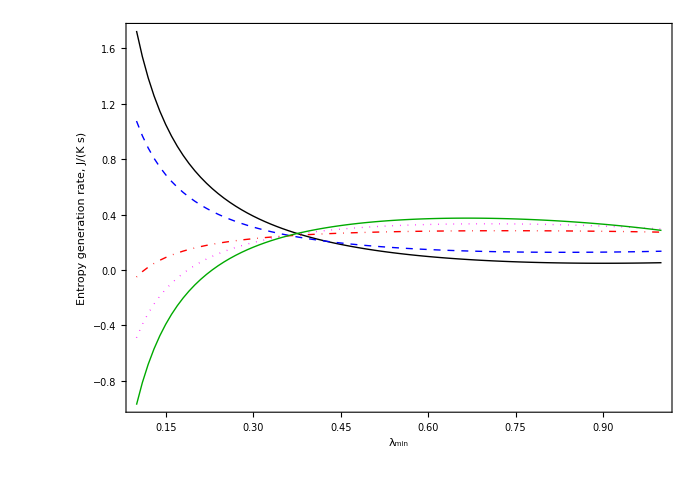

```mathematica
Quiet[Needs["PlotLegends`"]];
Clear[Legend0]
Legend0[size_,pos_]:={{{Graphics[{Black,Thick,Line[{{0,0},{3,0}}]}],Text[Style["trc=2.7",FontSize->18,FontFamily->"Arial",Black]]},{Graphics[{Blue,Dashed,Thick,Line[{{0,0},{3,0}}]}],Text[Style["trc=2.5",FontSize->18,FontFamily->"Arial",Blue]]},{Graphics[{Red,DotDashed,Thick,Line[{{0,0},{3,0}}]}],Text[Style["trc=2.2",FontSize->18,FontFamily->"Arial",Red]]},{Graphics[{Magenta,Dotted,Thick,Line[{{0,0},{3,0}}]}],Text[Style["trc=2.1",FontSize->18,FontFamily->"Arial",Magenta]]},{Graphics[{Darker[Green],Thick,Line[{{0,0},{3,0}}]}],Text[Style["trc=2",FontSize->18,FontFamily->"Arial",Darker[Green]]]}},LegendShadow->False,LegendSize->size,LegendPosition->pos,LegendTextSpace->3,LegendBorder->False};
PA=ShowLegend[ListPlot[{soltr2p7,soltr2p5,soltr2p2,soltr2p1,soltr2},PlotRange->All,Frame->True,Axes->True,BaseStyle->22,Joined->True,AspectRatio->0.7,PlotStyle->{{Thick,Black},{Thick,Blue,Dashed},{Thick,Red,DotDashed},{Thick,Magenta,Dotted},{Thick,Darker[Green]},{Thick,Yellow},{Thick,Brown},{Thick,Pink}},ImageSize->700,FrameLabel->{"λ_min","Entropy generation rate, J/(K s)"},AspectRatio->0.7],Legend0[{0.4,0.33},{0.2,0.3}]]
```